Accurate numerical simulation of radiation reaction effects in strong electromagnetic fields

N.V. Elkina, A.M. Fedotov, C. Herzing, H. Ruhl, arXiv 1401.7881
Notebook: Óscar Amaro, December 2023

## Figure 1

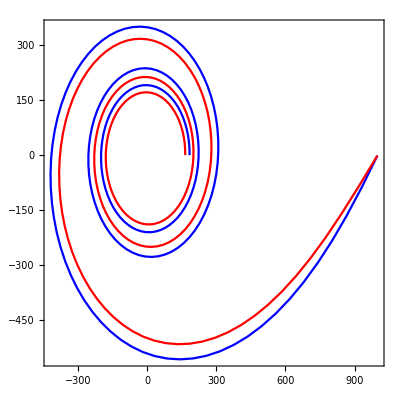

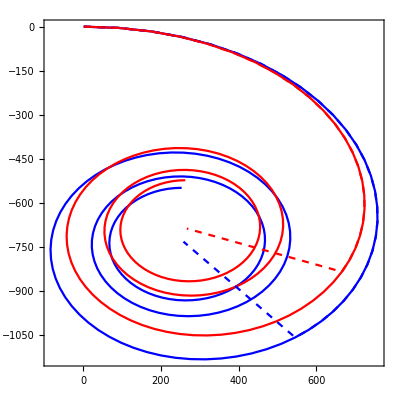

```mathematica
Clear[x, y, ϕ, uprp0, Κ, eq2150, exp, σ, γ0, u7, u9,xy7,xy9,c,m,e,cΩ7,cΩ9]

(* numerical precision for analytical eq30 is not enough... *)

c=3 10^8;
m=9.1 10^-31;
e=1.6 10^-19;
σ = +1;(*positron, to follow clockwise reotation*)
γ0 = 
  10^3;(*initial energy*)
uprp0 = 
 Sqrt[(γ0)^2 - 1];(*initial perpendicular momentum*)

Κ = 7.6 10^-7;
cΩ7=1;(*1/2 m/e^2 (10^-3 ) Κ; normalization of coordinates *)
exp=σ/uprp0 Sqrt[(1+uprp0^2)Exp[2Κ ϕ]-uprp0^2]Exp[I(0-σ ϕ)]Hypergeometric2F1[1,1/2-(I σ)/(2Κ),1-(I σ)/(2Κ),(1+uprp0^2)/uprp0^2 Exp[2Κ ϕ]];(*eq30*)
exp0=Limit[exp,ϕ->0];
xy7 = (exp-exp0)//Simplify;
u7 = 1/Sqrt[(1 + uprp0^2) Exp[2 Κ ϕ] - 
     uprp0^2] {uprp0 Cos[-σ ϕ], 
    uprp0 Sin[-σ ϕ]};(*eq29*)
x7[ϕϕ_] := NIntegrate[u7[[1]], {ϕ, 0, ϕϕ}]
y7[ϕϕ_] := NIntegrate[u7[[2]], {ϕ, 0, ϕϕ}]

Κ = 9.5 10^-7;
cΩ9=1;(*1/2 m/e^2 (10^-3 ) Κ;*)
exp=σ/uprp0 Sqrt[(1+uprp0^2)Exp[2Κ ϕ]-uprp0^2]Exp[I(0-σ ϕ)]Hypergeometric2F1[1,1/2-(I σ)/(2Κ),1-(I σ)/(2Κ),(1+uprp0^2)/uprp0^2 Exp[2Κ ϕ]];(*eq30*)
exp0=Limit[exp,ϕ->0];
xy9= (exp-exp0)//Simplify;
u9 = 1/Sqrt[(1 + uprp0^2) Exp[2 Κ ϕ] - 
     uprp0^2] {uprp0 Cos[-σ ϕ], 
    uprp0 Sin[-σ ϕ]};(*eq29*)
x9[ϕϕ_] := NIntegrate[u9[[1]], {ϕ, 0, ϕϕ}]
y9[ϕϕ_] := NIntegrate[u9[[2]], {ϕ, 0, ϕϕ}]

(* momenta *)
ParametricPlot[{{u7[[1]], u7[[2]]}, {u9[[1]], u9[[2]]}}, {ϕ, 
   0.001, 2 π 3 }, AspectRatio -> 1, Frame -> True, 
  PlotRange -> All, PlotStyle -> {Blue, Red}, PlotPoints -> 4] // Quiet

(* coordinates *)
ParametricPlot[{{cΩ7 x7[ϕ],cΩ7  y7[ϕ]}, {cΩ9 x9[ϕ], 
    cΩ9 y9[ϕ]}, {cΩ7 Im[xy7], -cΩ7 Re[xy7]}, {cΩ9 Im[xy9], -cΩ9 Re[xy9]}}, {ϕ, 
   0.001, 2 π 3 }, AspectRatio -> 1, Frame -> True, 
  PlotRange -> All, 
  PlotStyle -> {Blue, Red, {Blue, Dashed}, {Red, Dashed}}, 
  PlotPoints ->4] // Quiet
```